This is solution to the analytical description of the moving heat source. This solution is implementation of the paper:
 https://www.researchgate.net/publication/278683104_Analytical_Approximate_Solution_for_Double_Ellipsoidal_Heat_Source_in_Finite_Thick_Plate

Temperature Field solution based on Green’s function for Instantaneous Point Source:
dT(x,y,z,t’) = (δQ(x',y',z')dt')/(ρc(4π(t-t')))^(3/2) exp(((x-x')^2+(y-y')^2+(z-z')^2)/(4a(t-t')))
we are trying to find solution to the Single Ellipsoidal Heat Source of type:
Q(x,y,z)=(6√3η V I)/(a b c π√π)exp(-3 x^2/c^2-3 y^2/a^2-3 z^2/b^2)

The parameters for uniform source term are:

```mathematica
ρ = 4450; (*density in kg/m^3 *)
cp = 546;(* specific heat in J/kg K *)
k = 6 ; (*conductivity W/m K *)
ah =ch = 0.000075; (* laser dimension in m *)
bh = 0.00005; (* laser dimension in m *)

P = 100;
η = 0.8;
T0 = 298;
```

```mathematica
κ = k/(ρ cp);
```

```mathematica
Q[x_,y_,z_,a_,b_,c_,P_,η_]:=(6√3η P)/(a b c π√π)exp(-3 x^2/c^2-3 y^2/a^2-3 z^2/b^2)
```

```mathematica
ℰℒ[L_,x_,c_,t_,ts_]:=( Erf[((12 κ(t-ts)+c^2)(L-x)-c^2 x)/(c Sqrt[4κ(t-ts)] Sqrt[12κ(t-ts)+c^2])]+Erf[((12 κ(t-ts)+c^2)(L+x)-c^2 x)/(c Sqrt[4κ(t-ts)] Sqrt[12κ(t-ts)+c^2])])/(Erf[((L-x)√3)/c]+Erf[((L+x)√3)/c])
```

```mathematica
ℰℬ[B_,y_,a_,t_,ts_]:=( Erf[((12 κ(t-ts)+a^2)(B-y)-a^2 y)/(a Sqrt[4κ(t-ts)] Sqrt[12κ(t-ts)+a^2])]+Erf[((12 κ(t-ts)+a^2)(B+y)-a^2 y)/(a Sqrt[4κ(t-ts)] Sqrt[12κ(t-ts)+a^2])])/(Erf[((B-y)√3)/a]+Erf[((B+y)√3)/a])
```

```mathematica
ℰ𝒟[𝒟_,z_,b_,t_,ts_]:=( Erf[(12 κ(t-ts)𝒟+b^2(𝒟-z))/(b Sqrt[4κ(t-ts)] Sqrt[12κ(t-ts)+b^2])]+Erf[(b z)/(Sqrt[4κ(t-ts)] Sqrt[12κ(t-ts)+b^2])])/(Erf[(𝒟√3)/b])
```

Calculate the total integral to get the temperature distribution of the sample:

```mathematica
T[x_,y_,z_,t_, a_,b_,c_, L_, 𝒟_, B_, v_] := T0 + (3√3 P)/(ρ cp π√π) NIntegrate[ℰℒ[L,x-v ts, c,t,ts]*ℰℬ[B,y,a,t,ts]*ℰ𝒟[𝒟,z,b,t,ts]/(Sqrt[12 κ(t-ts)+a^2]Sqrt[12 κ(t-ts)+b^2]Sqrt[12 κ(t-ts)+c^2])
Exp[(-3(x-v ts)^2)/(12 κ(t-ts)+c^2)-(3 y^2)/(12 κ(t-ts)+a^2)-(3 z^2)/(12 κ(t-ts)+b^2)],{ts,0.0000001,t},MinRecursion->2]
```

```mathematica
T[1 10^-5,1 10^-5,1 10^-5,0.1,ah,bh,ch, 0.2,0.2,0.2, 0.21]
```

330.333

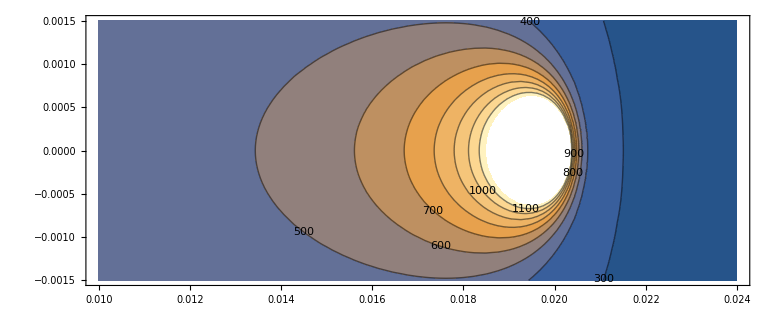

```mathematica
ContourPlot[T[x,y,0.0,2.,ah,bh,ch,10 10^-2,10 10^-2,5 10^-2,0.01],{x,2*0.5*10^-2,2*1.2 10^-2},{y,-15 10^-4,15 10^-4},ContourLabels->True,AspectRatio->True]
```

Same of the 3d plot:

```mathematica
Plot3D[T[x,y,0.0,1,ah,bh,ch,3 10^-2,5 10^-2,5 10^-2,0.01],{x,0.5*10^-2,1.2 10^-2},{y,-15 10^-4,15 10^-4}, PlotRange->{200,2500},AspectRatio->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

Export data to the text file:

```mathematica
xmin = 2*0.5*10^-2; xmax = 2*1.2 10^-2; nx = 100; (* maximum and minimum size of the domain and number of steps *)
ymin = -15 10^-4; ymax = 15 10^-4; ny = 100;
temperature = Table[T[x,y,0.0,2.,ah,bh,ch,10 10^-2,10 10^-2,5 10^-2,0.01],{x,xmin,xmax,(xmax-xmin)/nx},{y,ymin,ymax,(ymax-ymin)/ny}];
Export["TemperatureMovingHeatElliptic.csv", temperature]
```

TemperatureMovingHeatElliptic.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["TemperatureMovingHeatElliptic.csv"]]]
```